# Centrifuge problem (supplementary code)

### Finding the roots

```mathematica
MyFindRoots[1,5]
```

{1,ⅇ^((2 ⅈ π)/5),ⅇ^((4 ⅈ π)/5),ⅇ^(-(4 ⅈ π)/5),ⅇ^(-(2 ⅈ π)/5)}

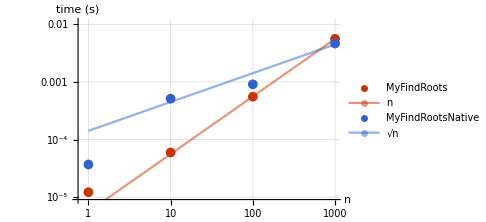

```mathematica
Needs["GeneralUtilities`"]
f1=MyFindRoots[1,#]&;
f2=MyFindRootsNative[1,#]&;
BenchmarkPlot[{f1,f2},#&,PowerRange[1,1000],"IncludeFits"->True]
```

### Checking valid subsets

```mathematica
RootsSetR=MyFindRoots[1,4]
```

{1,ⅈ,-1,-ⅈ}

```mathematica
RootSubsetsS=Subsets[RootsSetR,Length[RootsSetR]]
```

{{},{1},{ⅈ},{-1},{-ⅈ},{1,ⅈ},{1,-1},{1,-ⅈ},{ⅈ,-1},{ⅈ,-ⅈ},{-1,-ⅈ},{1,ⅈ,-1},{1,ⅈ,-ⅈ},{1,-1,-ⅈ},{ⅈ,-1,-ⅈ},{1,ⅈ,-1,-ⅈ}}

```mathematica
FindCentrifugeSols[4]
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ},{1,-1}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

### Reducing the solutions

```mathematica
RotateSol[4,1,{I,1,-I,-1}]
RotateSol[4,4,{I,1,-I,-1}]
```

{-1,ⅈ,1,-ⅈ}

{ⅈ,1,-ⅈ,-1}

```mathematica
SortSetClockwise[{I,1,-I,-1}]
SortSetClockwise[{-I,1,I,-1}]
```

{-ⅈ,1,ⅈ,-1}

{-ⅈ,1,ⅈ,-1}

```mathematica
(*ClassifyCentrifugeSols[4]*)
FindCentrifugeSols[4]
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ},{1,-1}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

```mathematica
ReduceCentrifugeSols[FindCentrifugeSols[4]]
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

## Drawings

### n = 4

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ},{1,-1}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

Roots for 4 holes: {-1,-ⅈ,ⅈ,1}

Solutions:

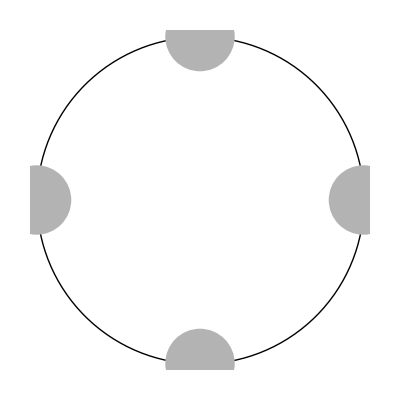
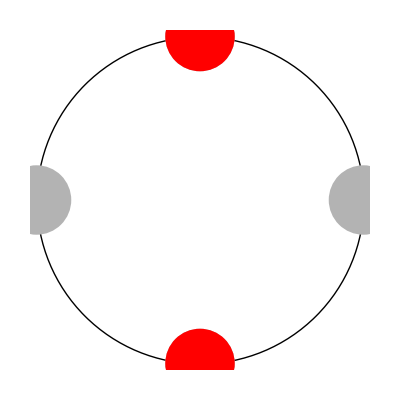
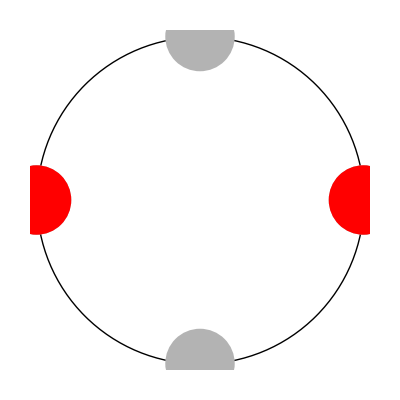
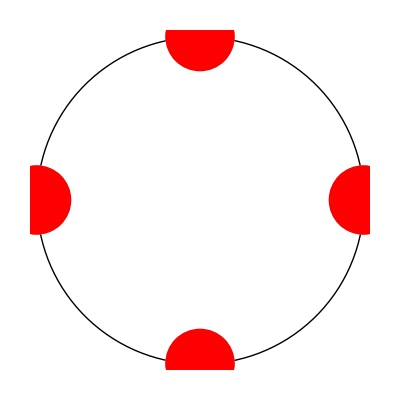
Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-,-Graphics-}
4 | {-Graphics-}

```mathematica
FindCentrifugeSols[4]
FindCentrifugeSols[4]//DrawCentrifugeSols
```

```mathematica
FindCentrifugeSols[4] //ReduceCentrifugeSols
FindCentrifugeSols[4] //ReduceCentrifugeSols//DrawCentrifugeSols
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

Roots for 4 holes: {-1,-ⅈ,ⅈ,1}

Solutions:

Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
4 | {-Graphics-}

```mathematica
ReduceCentrifugeSols[4]
DrawCentrifugeUniqueSols[4]
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{1,-1}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

Roots for 4 holes: {-1,-ⅈ,ⅈ,1}

Solutions:

Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
4 | {-Graphics-}

### n = 12

{{-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)},{{0,{{}}},{2,{{-ⅈ,ⅈ},{1,-1},{ⅇ^(-(ⅈ π)/6),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(ⅈ π)/3),ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^((ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^((ⅈ π)/6)}}},{3,{{-ⅈ,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),-1},{ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/6),ⅈ}}},{4,{{-ⅈ,1,ⅈ,-1},{-ⅈ,ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(ⅈ π)/6),1,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^((ⅈ π)/3),ⅈ},{ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((ⅈ π)/3),-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^((ⅈ π)/6),ⅈ},{ⅇ^(-(5 ⅈ π)/6),1,ⅇ^((ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3)}}},{5,{{-ⅈ,1,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),ⅈ,-1},{ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,1,ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/6),1,ⅈ,-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ}}},{6,{{-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((5 ⅈ π)/6),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅈ,ⅇ^((2 ⅈ π)/3),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,1,ⅇ^((ⅈ π)/3),ⅈ,-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,1,ⅇ^((ⅈ π)/6),ⅈ,-1},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3)}}},{7,{{-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,1,ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3)}}},{8,{{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)}}},{9,{{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),-1}}},{10,{{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{12,{{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}}}}

Roots for 12 holes: {-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)}

Solutions:

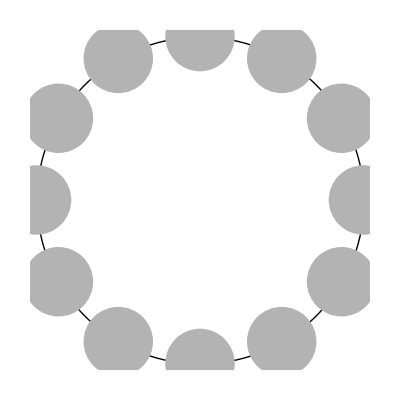
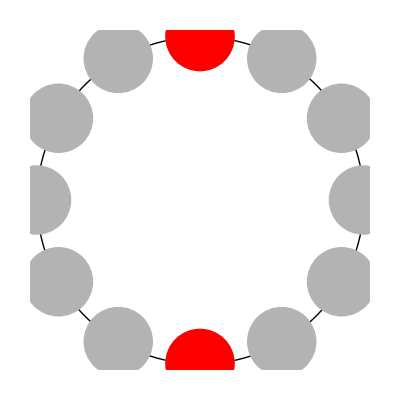
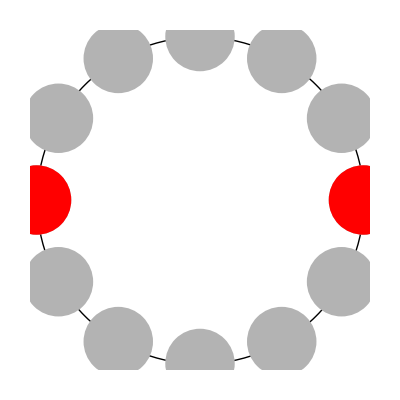
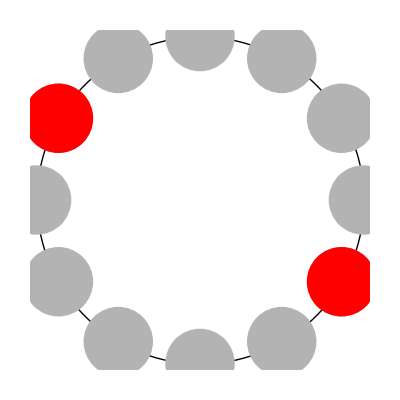
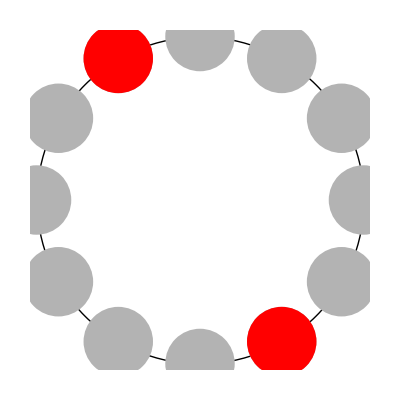
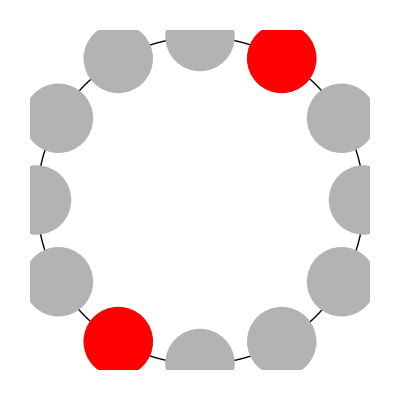
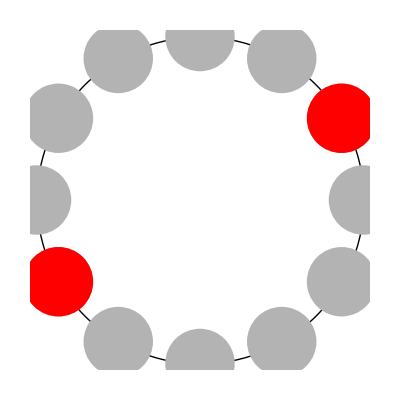
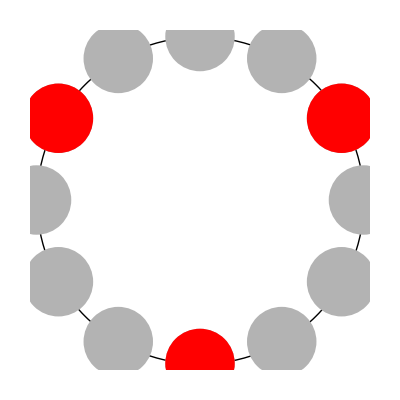
Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
3 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
10 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
12 | {-Graphics-}

```mathematica
FindCentrifugeSols[12]
FindCentrifugeSols[12]//DrawCentrifugeSols
```

```mathematica
FindCentrifugeSols[12] //ReduceCentrifugeSols
FindCentrifugeSols[12] //ReduceCentrifugeSols//DrawCentrifugeSols
```

{{-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)},{{0,{{}}},{2,{{-ⅈ,ⅈ}}},{3,{{-ⅈ,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6)}}},{4,{{-ⅈ,1,ⅈ,-1},{-ⅈ,ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3)}}},{5,{{-ⅈ,1,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6),-1}}},{6,{{-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((5 ⅈ π)/6),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅈ,ⅇ^((2 ⅈ π)/3),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1}}},{7,{{-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{8,{{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),-1}}},{9,{{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{10,{{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{12,{{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}}}}

Roots for 12 holes: {-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)}

Solutions:

Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
3 | {-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-}
10 | {-Graphics-}
12 | {-Graphics-}

## Computation time

### Benchmarking

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
f1=FindCentrifugeSols[#]&;
f2=ReduceCentrifugeSols[FindCentrifugeSols[#]]&;
BenchmarkPlot[{f1,f2},#&,Range[20],"IncludeFits"->True,TimeConstraint->500]
```

-Graphics-